# Chapter 6

## Example 6.1

```mathematica
Remove["Global`*"]

soln1=DSolve[{x''[t]+ω^2*x[t]==0},x[t],t];
Print["The solution of the homogeneous ODE is:"]
Print["x(t) = ",x[t]/.soln1[[1]]]
```

The solution of the homogeneous ODE is:

x(t) = C[1] Cos[t ω]+C[2] Sin[t ω]

```mathematica
soln2=DSolve[{x''[t]+ω^2*x[t]==0,x[0]==x0,x'[0]==v0},x[t],t];
Print["The solution of the ODE with initial conditions is:"]
Print["x(t) = ",x[t]/.soln2[[1]]//Simplify]
```

The solution of the ODE with initial conditions is:

x(t) = x0 Cos[t ω]+(v0 Sin[t ω])/ω

## Example 6.2

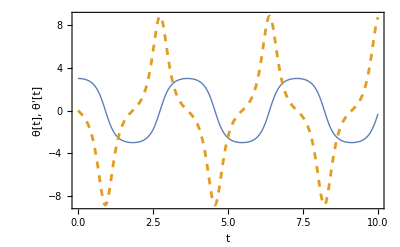

```mathematica
Remove["Global`*"]

SetOptions[Plot,Frame->True,Axes->True,BaseStyle->FontSize->20,PlotRange->All];

L=0.5;g=9.8;
soln=NDSolve[{θ''[t]+g/L*Sin[θ[t]]==0,θ'[0]==0,θ[0]==3},θ,{t,0,10}];

Plot[Evaluate[{θ[t],θ'[t]}/. soln],{t,0,10} ,FrameLabel->{"t","θ[t], θ'[t]"},PlotStyle->{Thick,Dashed}]
```

## Example 6.3

```mathematica
Remove["Global`*"]

Print["The general solution for underdamped and overdamped motion is:"]
Print[DSolve[{m*x''[t]+b*x'[t]+k*x[t]==0},x[t],t][[1,1]]]
Print[]

Print["The general solution for critically damped motion is: "]
Print[DSolve[{m*x''[t]+b*x'[t]+b^2/(4*m)*x[t]==0},x[t],t][[1,1]]]
```

The general solution for underdamped and overdamped motion is:

x[t]→ⅇ^(1/2 (-b/m-(√(b^2-4 k m))/m) t) C[1]+ⅇ^(1/2 (-b/m+(√(b^2-4 k m))/m) t) C[2]

The general solution for critically damped motion is:

x[t]→ⅇ^(-(b t)/(2 m)) C[1]+ⅇ^(-(b t)/(2 m)) t C[2]

## Example 6.4

```mathematica
Remove["Global`*"]

Print["Solution for underdamped is:"];
m=1;b=1;k=1;
DSolve[{m*x''[t]+b*x'[t]+k*x[t]==0},x[t],t]
Print[]

Print["Solution for overdamped is: "];
m=1;b=3;k=1;
DSolve[{m*x''[t]+b*x'[t]+k*x[t]==0},x[t],t]
Print[]

Print["Solution for critically damped is: "];
m=1;k=1;b=2*Sqrt[k*m];
DSolve[{m*x''[t]+b*x'[t]+k*x[t]==0},x[t],t]
```

Solution for underdamped is:

{{x[t]→ⅇ^(-t/2) C[2] Cos[(√3 t)/2]+ⅇ^(-t/2) C[1] Sin[(√3 t)/2]}}

Solution for overdamped is:

{{x[t]→ⅇ^((-3/2-(√5)/2) t) C[1]+ⅇ^((-3/2+(√5)/2) t) C[2]}}

Solution for critically damped is:

{{x[t]→ⅇ^-t C[1]+ⅇ^-t t C[2]}}

## Example 6.5

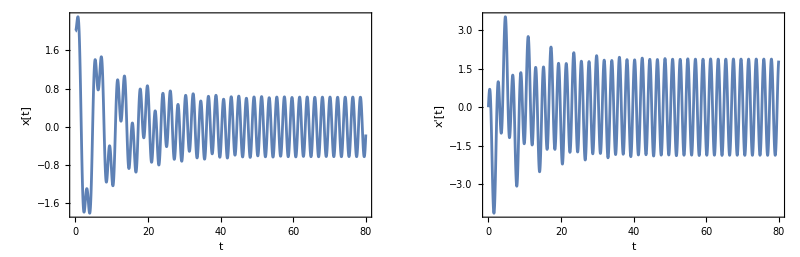

```mathematica
Remove["Global`*"]

SetOptions[Plot,Frame->True,Axes->True,BaseStyle->FontSize->20,PlotRange->All];

m=1;k=1;b=.2;
d=5;ω=3;
soln=NDSolve[{m*x''[t]+b*x'[t]+k*x[t]==d*Cos[ω*t],x[0]==2,x'[0]==0},x,{t,0,80}];

gr1=Plot[Evaluate[{x[t]}/. soln],{t,0,80} ,FrameLabel->{"t","x[t]"}];
gr2=Plot[Evaluate[{x'[t]}/. soln],{t,0,80} ,FrameLabel->{"t","x'[t]"}];
GraphicsGrid[{{gr1,gr2}}]
```

## Example 6.6

ⅇ^(-t (γ+√(γ^2-ωo^2))) C[1]+ⅇ^(t (-γ+√(γ^2-ωo^2))) C[2]+(Fo ((-ω^2+ωo^2) Cos[t ω]+2 γ ω Sin[t ω]))/(m (4 γ^2 ω^2+(ω^2-ωo^2)^2))

(Fo ((-ω^2+ωo^2) Cos[t ω]+2 γ ω Sin[t ω]))/(m (4 γ^2 ω^2+(ω^2-ωo^2)^2))

ⅇ^(-t (γ+√(γ^2-ωo^2))) C[1]+ⅇ^(t (-γ+√(γ^2-ωo^2))) C[2]

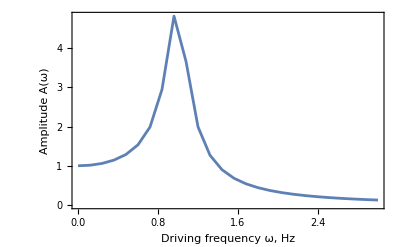

```mathematica
Remove["Global`*"]

sol=DSolve[{x''[t]+ωo^2*x[t]+2*γ*x'[t]==Fo/m*Cos[ω*t]},x[t],t];
x=x[t]/.sol[[1]]//Simplify
steady=x/.Exp[t_]->0

trans=x-steady
m=1;γ=0.1;Fo=1;ωo=1;
u=Table[{ω,NMaxValue[steady,t]},{ω,0,3,.12}];

ListPlot[u,FrameLabel->{"Driving frequency ω, Hz","Amplitude A(ω)"},
Frame->True,BaseStyle->{FontSize->16},Joined->True]
```

## Example 6.7

ⅇ^(-t (γ+√(γ^2-ωo^2))) C[1]+ⅇ^(t (-γ+√(γ^2-ωo^2))) C[2]+(Fo ((-ω^2+ωo^2) Cos[t ω]+2 γ ω Sin[t ω]))/(m (4 γ^2 ω^2+(ω^2-ωo^2)^2))

(Fo ((-ω^2+ωo^2) Cos[t ω]+2 γ ω Sin[t ω]))/(m (4 γ^2 ω^2+(ω^2-ωo^2)^2))

(Fo^2 ((-ω^2+ωo^2) Cos[t ω]+2 γ ω Sin[t ω])^2)/(2 m (4 γ^2 ω^2+(ω^2-ωo^2)^2)^2)

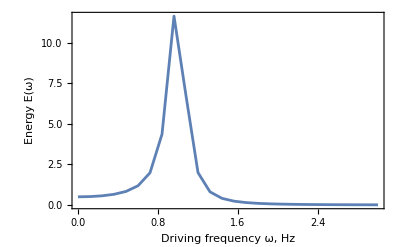

```mathematica
Remove["Global`*"]

sol=DSolve[{x''[t]+ωo^2x[t]+2γ x'[t]==Fo/m Cos[ω t]},x[t],t];
x=x[t]/.sol[[1]]//Simplify
steady=x/.Exp[t_]->0

en=1/2*m*steady^2

m=1;γ=0.1;Fo=1;ωo=1;
u=Table[{ω,NMaxValue[en,t]},{ω,0,3,0.12}];

ListPlot[u,PlotRange->All,FrameLabel->{"Driving frequency ω, Hz","Energy E(ω)"},
Frame->True,BaseStyle->{FontSize->16},Joined->True]
```

## Example 6.8

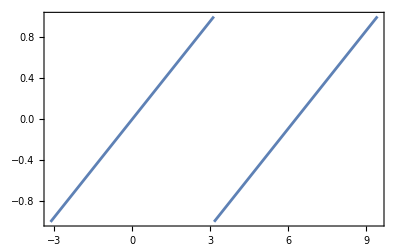

```mathematica
Remove["Global`*"]

f=Piecewise[{{x/Pi,x>-Pi&&x<Pi},{(x-2*Pi)/Pi,x>Pi&&x<3*Pi}}];
Plot[f,{x,-π,3*π},PlotRange->All]
```

```mathematica
T=2*Pi;numTerms=30;
Print["ao=",ao=(2/T)*Integrate[f,{x,0,T}]];

an:=(2/T)*Integrate[f*Cos[2*n*Pi*x/T],{x,0,T}];
bn:=(2/T)*Integrate[f*Sin[2*n*Pi*x/T],{x,0,T}];
Print["an-Fourier coefficients=",an];
Print["bn-Fourier coefficients=",bn];
```

ao=0

an-Fourier coefficients=(-1+Cos[2 n π]+2 n π Sin[n π])/(n^2 π^2)

bn-Fourier coefficients=(-2 n π Cos[n π]+Sin[2 n π])/(n^2 π^2)

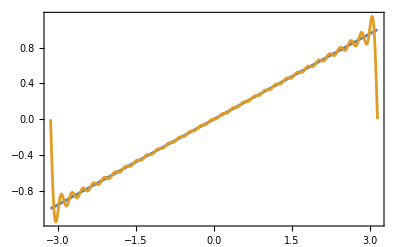

```mathematica
anList=Table[an/.n->m,{m,1,numTerms}];bnList=Table[bn/.n->m,{m,1,numTerms}];Plot[{f,ao/2+∑_(n=1)^Length[anList] (anList[[n]]*Cos[2*n*Pi*x/T])+∑_(n=1)^Length[bnList] (bnList[[n]]*Sin[2*n*Pi*x/T])},{x,-T/2,T/2}]
```

## Figure 6.14

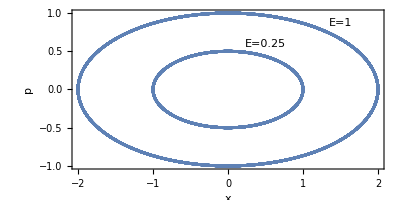

```mathematica
Remove["Global`*"]
A=1;ωd=1;ϕ=0;m=0.5;
x=A*Cos[ωd*t-ϕ];
p=m*D[x,t];
gr1=ParametricPlot[{x,p},{t,0,100},FrameLabel->{"x","p"},Frame->True,BaseStyle->{FontSize->16},PlotRange->All];

A=2;ωd=1;ϕ=0;
x=A*Cos[ωd*t-ϕ];
p=m*D[x,t];
gr2=ParametricPlot[{x,p},{t,0,100},FrameLabel->{"x","p"},Frame->True,BaseStyle->{FontSize->16},PlotRange->All];

rText=Text["E=0.25",{0.5,0.6}];
cText=Text["E=1",{1.5,0.87}];
txt=Graphics[{cText,rText}];
Show[{gr1,gr2,txt},PlotStyle->{Default,Dashed}]
```

## Example 6.9

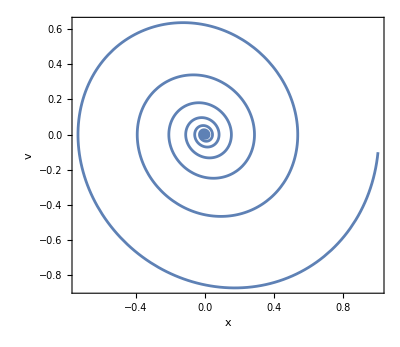

```mathematica
Remove["Global`*"]

A=1;ωd=1;ϕ=0;γ=0.1;
x=A*Exp[-γ*t]*Cos[ωd*t-ϕ];
v=D[x,t];

ParametricPlot[{x,v},{t,0,100},FrameLabel->{"x","v"},Frame->True,BaseStyle->{FontSize->16},PlotRange->All]
```